### init

```mathematica
basedir="\\\\192.168.1.21\\d\\data\\Cycle 197\\exp_3-16-19\\rawdata\\sc\\";
Get[basedir<>"..\\camera_ifg.m"]
minIntens=2000;  (* Schwellenwert zur Unterdrückung schwach beleuchtetet Randbereiche der Kamera *)
(*
loadimage[basedir<>filename]    liefert Array mit den einzelnen Bildern aus der Tiff-Datei.;
fittile[images_,tileDX_,tileDY_,nx_,ny_,minIntensity_,period_]

*)
```

```mathematica
LoadDatFile[filename_]:=  ToExpression[Transpose[StringSplit[#,"\t"] & /@ Pick[#,StringMatchQ[#,{"\\**","[*"," *","\t*",""}],False]&@Import[basedir<>filename,"lines"]]]
```

```mathematica
reduceSlotsBy[img_,its_,slotmax_]:=Module[{maxph,maxtim},
maxtim=slotmax/its;
maxph=Length[img]/(slotmax+2);
Flatten[Table[    Join[{img[[1+(ph-1)*(slotmax+2)]]},Table[Total[img[[(ph-1)*(slotmax+2)+1+(tim-1)*its;;(ph-1)*(slotmax+2)+tim*its]],1],{tim,1,maxtim}],{img[[ph*(slotmax+2)]]}]     ,{ph,1,maxph}],1]
]
```

```mathematica
(* alle Bilder eines Multi-Page-Images aufsummieren und auf die Anzahl der nicht leeren Pixel normieren *)
integrateImg[img_]:=(Total[#,2]&/@img)   / Count[Flatten[Total[img]],x_/;x>10]
(*integrateImg[img_]:=(Total[#,2]&/@img)   / (Length[img[[1]]]*Length[img[[1,1]]])*)
```

```mathematica
(* counts per pixel *)
cpp[img_]:=N[Total[img,2]  / (Times @@ Dimensions[img])];
```

# 30° double loop IFM, on glass block + felt

```mathematica
filename = "ifg3p120s_16Jun1643.tif";
```

{12,50,50}

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{1.07427,0,-595.346}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit :: sszero will be suppressed during this calculation.

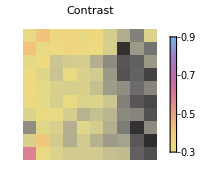
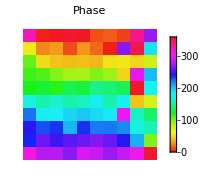
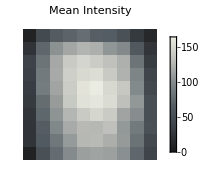
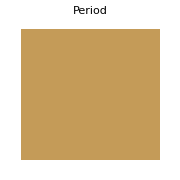

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1]]], Length[img[[1,1]]] ,1,9][[3;;5]]
res=fitgrid[img,5,5,1,-8.6];
plotres[res]
```

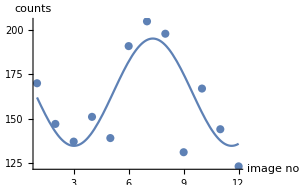
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 164.942 | 5.47793 | 30.1102 | 2.40378×10^-10
CameraIfgPackage`Private`b | 30.3232 | 7.53889 | 4.02224 | 0.00300789
CameraIfgPackage`Private`d | 2.50927 | 0.255459 | 9.82259 | 4.15232×10^-6contr=0.183842
offs=164.942
phase=143.771°
period=8.6

```mathematica
showtileres[res,5,5]
```

```mathematica
filename = "ifg3p120s_16Jun1720.tif";
```

{14,50,50}

{0.0656182,10324.8,7.63761}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

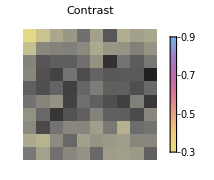
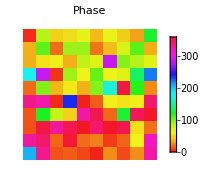
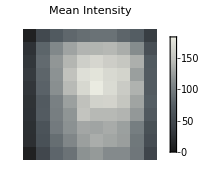
-Graphics--Graphics--Graphics--Graphics-

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1]]], Length[img[[1,1]]] ,1,9][[3;;5]]
res=fitgrid[img,5,5,1,-8.6];
plotres[res]
```

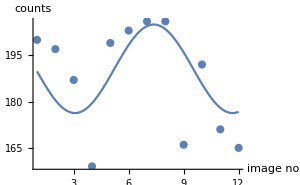
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 190.627 | 4.5899 | 41.5317 | 1.35583×10^-11
CameraIfgPackage`Private`b | 14.3443 | 6.3489 | 2.25933 | 0.0502316
CameraIfgPackage`Private`d | 2.46926 | 0.446463 | 5.53072 | 0.000365395contr=0.0752479
offs=190.627
phase=141.478°
period=8.6

```mathematica
showtileres[res,5,5]
```

# 30° double loop IFM, on standard plastic support

```mathematica
filename = "ifg1_3p120s_16Jun1903.tif";
```

{31,50,50}

{0.471474,10390.7,9.98202}

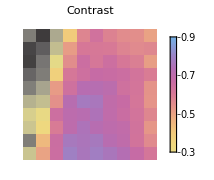
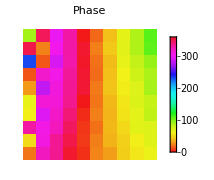
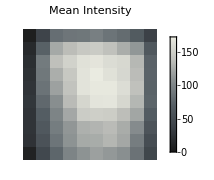
-Graphics--Graphics--Graphics--Graphics-

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1]]], Length[img[[1,1]]] ,1,9][[3;;5]]
res=fitgrid[img,5,5,1.2,-totalres[[3]]];
plotres[res]
```

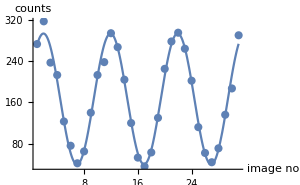
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 166.708 | 2.61179 | 63.8289 | 7.14411×10^-32
CameraIfgPackage`Private`b | 126.636 | 3.70175 | 34.2098 | 2.18523×10^-24
CameraIfgPackage`Private`d | 0.33947 | 0.027405 | 12.3872 | 7.0173×10^-13contr=0.759631
offs=166.708
phase=19.4502°
period=9.98202

```mathematica
showtileres[res,5,4]
```

```mathematica
filename = "ifg1_3p360s_16Jun2012.tif";
```

{31,50,50}

{0.494518,30344.,10.1153}

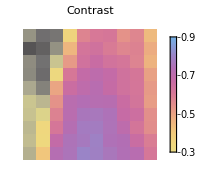
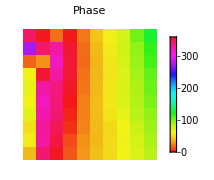
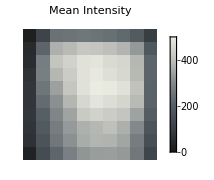
-Graphics--Graphics--Graphics--Graphics-

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1]]], Length[img[[1,1]]] ,1,9][[3;;5]]
res=fitgrid[img,5,5,1.2,-totalres[[3]]];
plotres[res]
```

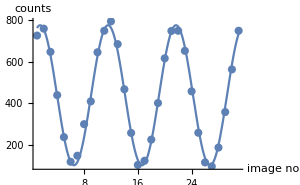
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 439.363 | 4.28157 | 102.617 | 1.2733×10^-37
CameraIfgPackage`Private`b | 334.87 | 6.0575 | 55.2818 | 3.87955×10^-30
CameraIfgPackage`Private`d | 0.66734 | 0.017049 | 39.1424 | 5.42149×10^-26contr=0.762172
offs=439.363
phase=38.2358°
period=10.1153

```mathematica
showtileres[res,5,3]
```

```mathematica
filename = "ifg1_3p120s_16Jun2326.tif";
```

{31,50,50}

{0.50344,10236.,10.0864}

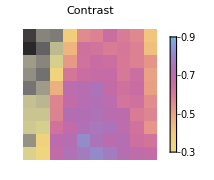
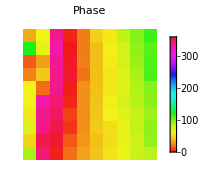
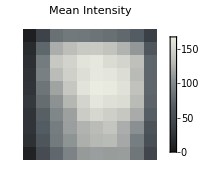
-Graphics--Graphics--Graphics--Graphics-

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1]]], Length[img[[1,1]]] ,1,9][[3;;5]]
res=fitgrid[img,5,5,1.2,-totalres[[3]]];
plotres[res]
```

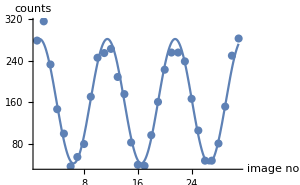
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 162.408 | 3.08487 | 52.6464 | 1.50414×10^-29
CameraIfgPackage`Private`b | 119.637 | 4.36749 | 27.3925 | 9.23979×10^-22
CameraIfgPackage`Private`d | 0.713541 | 0.0343901 | 20.7484 | 1.54434×10^-18contr=0.736644
offs=162.408
phase=40.8829°
period=10.0864

```mathematica
showtileres[res,5,4]
```

```mathematica
filename = "ifg1_3p360s_17Jun0035.tif";
```

{31,50,50}

{0.508826,31052.3,10.0461}

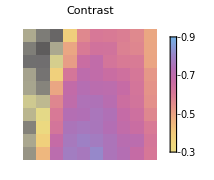
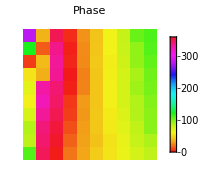
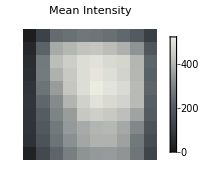
-Graphics--Graphics--Graphics--Graphics-

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1]]], Length[img[[1,1]]] ,1,9][[3;;5]]
res=fitgrid[img,5,5,1.2,-totalres[[3]]];
plotres[res]
```

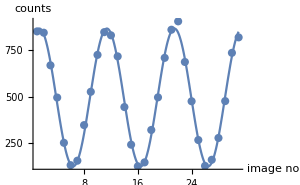
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 496.458 | 4.41925 | 112.34 | 1.01559×10^-38
CameraIfgPackage`Private`b | 369.887 | 6.21338 | 59.5307 | 4.96244×10^-31
CameraIfgPackage`Private`d | 0.727448 | 0.01603 | 45.3805 | 9.18306×10^-28contr=0.745053
offs=496.458
phase=41.6797°
period=10.0461

```mathematica
showtileres[res,5,4]
```

```mathematica
filename = "ifg1_3p120s_17Jun0348.tif";
```

{31,50,50}

{0.506418,10498.4,10.0638}

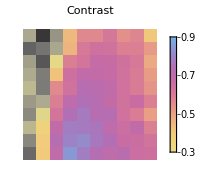
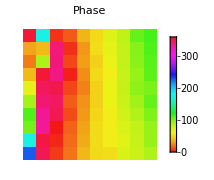
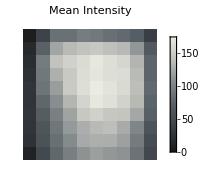
-Graphics--Graphics--Graphics--Graphics-

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1]]], Length[img[[1,1]]] ,1,9][[3;;5]]
res=fitgrid[img,5,5,1.2,-totalres[[3]]];
plotres[res]
```

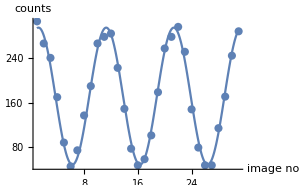
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 171.871 | 2.17833 | 78.9001 | 1.95049×10^-34
CameraIfgPackage`Private`b | 123.73 | 3.06582 | 40.3578 | 2.33645×10^-26
CameraIfgPackage`Private`d | 0.805444 | 0.023675 | 34.0208 | 2.54303×10^-24contr=0.719901
offs=171.871
phase=46.1485°
period=10.0638

```mathematica
showtileres[res,5,4]
```

```mathematica
filename = "ifg1_3p360s_17Jun0458.tif";
```

{31,50,50}

{0.504125,31522.8,10.0364}

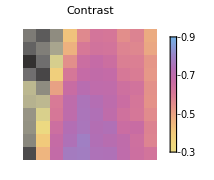
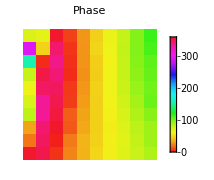
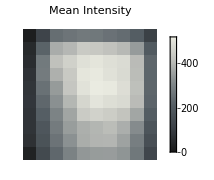
-Graphics--Graphics--Graphics--Graphics-

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1]]], Length[img[[1,1]]] ,1,9][[3;;5]]
res=fitgrid[img,5,5,1.2,-totalres[[3]]];
plotres[res]
```

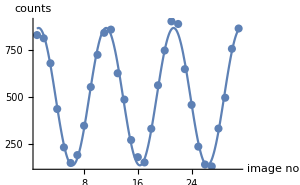
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 501.684 | 5.30929 | 94.4918 | 1.27425×10^-36
CameraIfgPackage`Private`b | 365.113 | 7.44115 | 49.0667 | 1.05853×10^-28
CameraIfgPackage`Private`d | 0.7906 | 0.019638 | 40.2586 | 2.50025×10^-26contr=0.727774
offs=501.684
phase=45.2981°
period=10.0364

```mathematica
showtileres[res,5,4]
```

```mathematica
filename = "ifg1_3p120s_17Jun0811.tif";
```

{23,50,50}

{0.475014,10399.1,10.0117}

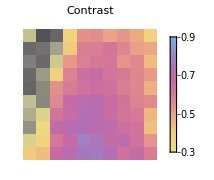
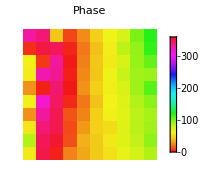
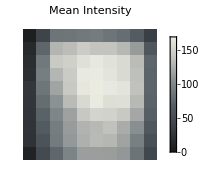
-Graphics--Graphics--Graphics--Graphics-

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1]]], Length[img[[1,1]]] ,1,9][[3;;5]]
res=fitgrid[img,5,5,1.2,-totalres[[3]]];
plotres[res]
```

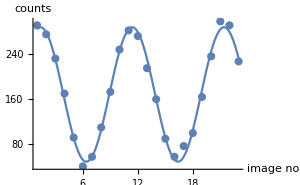
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 168.46 | 2.0888 | 80.649 | 1.29297×10^-26
CameraIfgPackage`Private`b | 119.058 | 2.87166 | 41.4597 | 7.1748×10^-21
CameraIfgPackage`Private`d | 0.707135 | 0.0234034 | 30.215 | 3.64748×10^-18contr=0.706746
offs=168.46
phase=40.5158°
period=10.0117

```mathematica
showtileres[res,5,4]
```

```mathematica
f1 = "singleimage1800s_18Jun1304.tif";
f2 = "singleimage1800s_18Jun1357.tif";
```

```mathematica
i1=loadimage[basedir<>f1][[1]]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
i2=loadimage[basedir<>f2][[1]]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
```

{0,2,3}

{0,2,3}

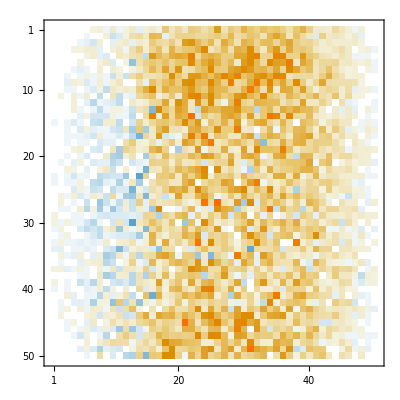

```mathematica
MatrixPlot[i2-i1]
```